# Highly divisible triangular number

The sequence of triangle numbers is generated by adding the natural numbers. So the 7th triangle number would be 1 + 2 + 3 + 4 + 5 + 6 + 7 = 28. The first ten terms would be:

1, 3, 6, 10, 15, 21, 28, 36, 45, 55, ...

Let us list the factors of the first seven triangle numbers:

1: 1
 3: 1,3
 6: 1,2,3,6
10: 1,2,5,10
15: 1,3,5,15
21: 1,3,7,21
28: 1,2,4,7,14,28

We can see that 28 is the first triangle number to have over five divisors.

What is the value of the first triangle number to have over five hundred divisors?

## counting divisors

```mathematica
DivisorSigma[0,28]
```

6

```mathematica
Asymptotic
```

```mathematica
Names["Asymptot*"]
```

{Asymptotic,AsymptoticDSolveValue,AsymptoticEqual,AsymptoticEquivalent,AsymptoticGreater,AsymptoticGreaterEqual,AsymptoticIntegrate,AsymptoticLess,AsymptoticLessEqual,AsymptoticOutputTracker,AsymptoticProduct,AsymptoticRSolveValue,AsymptoticSolve,AsymptoticSum}

```mathematica
Names["*Asymptot*"]
```

{Asymptotic,AsymptoticDSolveValue,AsymptoticEqual,AsymptoticEquivalent,AsymptoticGreater,AsymptoticGreaterEqual,AsymptoticIntegrate,AsymptoticLess,AsymptoticLessEqual,AsymptoticOutputTracker,AsymptoticProduct,AsymptoticRSolveValue,AsymptoticSolve,AsymptoticSum,DiscreteAsymptotic}

```mathematica
AsymptoticProduct[f,x,x->Subscript[x, 0]]
```

## Triangular Numbers

```mathematica
Accumulate[Range[100]]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325,351,378,406,435,465,496,528,561,595,630,666,703,741,780,820,861,903,946,990,1035,1081,1128,1176,1225,1275,1326,1378,1431,1485,1540,1596,1653,1711,1770,1830,1891,1953,2016,2080,2145,2211,2278,2346,2415,2485,2556,2628,2701,2775,2850,2926,3003,3081,3160,3240,3321,3403,3486,3570,3655,3741,3828,3916,4005,4095,4186,4278,4371,4465,4560,4656,4753,4851,4950,5050}

```mathematica
FindSequenceFunction[Accumulate[Range[100]]]
```

1/2 (#1+#1^2)&

```mathematica
FindSequenceFunction[Accumulate[Range[100]]][n ]
```

1/2 (n+n^2)

```mathematica
DiscreteAsymptotic[FindSequenceFunction[Accumulate[Range[100]]][n ],n]
```

n^2/2

## Example with solving for Fibonnaci numbers

```mathematica
DiscreteAsymptotic[Fibonacci[n ],n]
```

GoldenRatio^n/(√5)

```mathematica
NSolve[DiscreteAsymptotic[Fibonacci[n ],n]==4 10^6,n]
```

{{n→ConditionalExpression[2.07809 (16.0065+(0.+6.28319 ⅈ) C[1]), C[1]∈ℤ]}}

```mathematica
n/.{{n->ConditionalExpression[2.0780869212350273 (16.006523875301216+(0.+6.283185307179586 ⅈ) C[1]),C[1]∈Integers]}}
```

{ConditionalExpression[2.07809 (16.0065+(0.+6.28319 ⅈ) C[1]), C[1]∈ℤ]}

```mathematica
First[{ConditionalExpression[2.0780869212350273 (16.006523875301216+(0.+6.283185307179586 ⅈ) C[1]),C[1]∈Integers]}]
```

ConditionalExpression[2.07809 (16.0065+(0.+6.28319 ⅈ) C[1]), C[1]∈ℤ]

```mathematica
Names["*Discrete*"]
```

{DiscreteAsymptotic,DiscreteChirpZTransform,DiscreteConvolve,DiscreteDelta,DiscreteHadamardTransform,DiscreteIndicator,DiscreteLimit,DiscreteLQEstimatorGains,DiscreteLQRegulatorGains,DiscreteLyapunovSolve,DiscreteMarkovProcess,DiscreteMaxLimit,DiscreteMinLimit,DiscretePlot,DiscretePlot3D,DiscreteRatio,DiscreteRiccatiSolve,DiscreteShift,DiscreteTimeModelQ,DiscreteUniformDistribution,DiscreteVariables,DiscreteWaveletData,DiscreteWaveletPacketTransform,DiscreteWaveletTransform,ToDiscreteTimeModel}

```mathematica
RSolveValue[f[n-2] +f[n-1]==4*10^6∧f[1]==1∧f[0]==0,f[n],n]
```

RSolveValue::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

RSolveValue[f[-2+n]+f[-1+n]==4000000&&f[1]==1&&f[0]==0,f[n],n]

```mathematica
Fibonacci[1]
```

1

```mathematica
Fibonacci[2]
```

1

```mathematica
RSolveValue[{a[n+1]==2 a[n],a[0]==1},a[3],n]
```

8

```mathematica
RSolveValue[{f[1]==1, f[n-2] +f[n-1]==f[n],f[2]==1},f[3],n]
```

2

```mathematica
RSolveValue[{f[1]==1, f[n-2] +f[n-1]==f[n],f[2]==1},f[n],n]
```

Fibonacci[n]

## Fibonacci Inverse

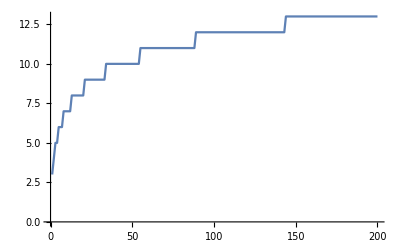

```mathematica
ListLinePlot[Table[NestWhile[(#+1)&,1,Fibonacci[#]≤n&],{n,200}]]
```

```mathematica
NestWhile[(#1+1)&,1,Fibonacci[#]≤4*10^6&,1,Infinity,-1]
```

33

```mathematica
Fibonacci[33]
```

3524578

```mathematica
NestWhile[(#1+1)&,1,Fibonacci[#]≤4*10^6&,1,Infinity,-1]
```

```mathematica
FindSequenceFunction[Accumulate[Range[100]]]
```

1/2 (#1+#1^2)&

```mathematica
DivisorSigma[0,Accumulate[Range[10]]]
```

{1,2,4,4,4,4,6,9,6,4}

```mathematica
NestWhile[FindSequenceFunction[Accumulate[Range[100]]],1,DivisorSigma[0,Accumulate[#]]≤500&]
```

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[1].

1

```mathematica
FindSequenceFunction[Accumulate[Range[100]]]
```

1/2 (#1+#1^2)&

```mathematica
NestWhile[#+1&,1,Function[n,DivisorSigma[0,FindSequenceFunction[Accumulate[Range[100]]][n]]≤500]]
```

$Aborted

```mathematica
NestWhile[#+1&,1,Function[n,DivisorSigma[0,FindSequenceFunction[Accumulate[Range[100]]][n]]≤6]]
```

8

```mathematica
Accumulate[Range[8]]
```

{1,3,6,10,15,21,28,36}

```mathematica
Function[n,DivisorSigma[0,FindSequenceFunction[Accumulate[Range[100]]][n]]]
```

Function[n,DivisorSigma[0,FindSequenceFunction[Accumulate[Range[100]]][n]]]

```mathematica
Function[n,DivisorSigma[0,FindSequenceFunction[Accumulate[Range[100]]][n]]][3]
```

4

```mathematica
Function[n,DivisorSigma[0,FindSequenceFunction[Accumulate[Range[100]]][n]]][Range[30]]
```

{1,2,4,4,4,4,6,9,6,4,8,8,4,8,16,8,6,6,8,16,8,4,12,18,6,8,16,8,8,8}

```mathematica
DivisorSigma[0,#]&/@Accumulate[Range[90]]
```

{1,2,4,4,4,4,6,9,6,4,8,8,4,8,16,8,6,6,8,16,8,4,12,18,6,8,16,8,8,8,10,20,8,8,24,12,4,8,24,12,8,8,8,24,12,4,16,24,9,12,16,8,8,16,24,24,8,4,16,16,4,12,36,24,16,8,8,16,16,8,18,18,4,12,24,16,16,8,16,40,10,4,16,32,8,8,24,12,12,24}

```mathematica
Position[DivisorSigma[0,#]&/@Accumulate[Range[1000]],40]
```

{{80},{95},{159},{160},{323},{404},{405},{415},{416},{479},{543},{544},{672},{736},{863},{890},{891},{992}}

```mathematica
Max[DivisorSigma[0,#]&/@Accumulate[Range[1000]]]
```

144

```mathematica
Max[DivisorSigma[0,#]&/@Accumulate[Range[100000]]]
```

1344

```mathematica
Position[DivisorSigma[0,#]&/@Accumulate[Range[100000]],500]
```

{}

```mathematica
Select[#>500&][DivisorSigma[0,#]&/@Accumulate[Range[100000]]]
```

{576,648,576,576,512,640,576,640,768,504,512,576,576,512,640,540,576,512,576,640,576,720,576,600,576,576,576,576,512,576,576,576,576,512,512,512,576,504,576,504,512,720,576,576,672,576,512,512,560,504,1024,576,576,504,576,512,672,576,576,720,576,768,672,896,576,672,768,576,640,768,576,576,576,576,576,512,512,768,576,576,512,512,540,720,600,576,640,640,576,576,576,768,576,576,512,576,864,768,1008,512,576,576,640,600,768,512,672,576,640,576,576,768,640,768,576,560,600,768,672,576,512,512,512,640,576,512,504,576,768,576,768,576,640,576,768,720,768,512,576,512,512,512,768,576,768,600,576,512,560,768,960,672,672,576,720,864,576,640,576,600,576,576,512,672,768,512,576,512,1008,576,640,512,576,576,640,576,512,512,512,960,720,1024,640,576,576,768,768,540,672,576,512,640,768,960,576,800,1024,576,576,640,512,576,512,672,512,864,512,576,648,648,576,1280,512,576,504,576,768,512,768,576,512,576,648,768,576,576,512,512,576,648,576,640,768,960,600,512,576,768,576,768,504,768,576,512,512,640,864,512,768,960,512,512,576,560,648,512,720,576,576,528,1024,576,640,512,512,576,672,512,512,576,640,576,576,1200,864,768,960,512,512,576,576,512,512,512,864,640,512,576,768,512,600,576,640,640,576,512,576,576,672,640,768,540,576,640,576,720,576,512,576,512,576,512,576,512,576,512,576,768,576,704,512,720,512,576,576,576,576,576,512,512,512,1344,512,768,512,1152,576,768,540,512,576,576,576,512}

```mathematica
FirstPosition[DivisorSigma[0,#]&/@Accumulate[Range[100000]],x_/;x>500]
```

{12375}

```mathematica
DivisorSigma[0,#]&/@Accumulate[Range[12380]]
```

{1,2,4,4,4,4,6,9,6,4,8,8,4,8,16,8,6,6,8,16,8,4,12,18,6,8,16,8,8,8,10,20,8,8,24,12,4,8,24,12,8,8,8,24,12,4,16,24,9,12,16,8,8,16,24,24,8,4,16,16,4,12,36,24,16,8,8,16,16,8,18,18,4,12,24,16,16,8,16,40,10,4,16,32,8,8,24,12,12,24,16,16,8,8,40,20,6,18,36,12,8,8,12,48,16,4,16,16,8,16,32,16,8,16,16,24,12,8,48,36,6,8,16,16,24,12,14,28,16,8,16,32,8,16,48,12,8,8,16,32,8,8,48,48,8,12,24,8,12,12,12,36,24,16,32,16,4,8,40,40,20,10,8,32,16,4,24,36,12,24,24,8,8,24,48,32,8,4,24,24,8,16,24,24,16,16,16,32,32,8,24,24,4,16,48,12,12,12,18,36,8,8,32,32,8,12,48,32,32,16,8,16,8,8,48,48,8,8,32,32,16,8,20,90,18,4,16,16,8,32,48,12,12,24,16,16,16,8,32,32,6,18,24,24,24,16,24,24,16,8,24,48,8,16,64,16,8,16,32,48,12,4,24,48,16,16,16,8,16,16,16,64,16,12,48,16,4,12,72,24,8,8,8,32,32,16,60,45,12,16,16,8,12,24,24,48,16,8,48,48,8,8,32,32,24,12,16,32,16,8,24,24,4,24,48,8,8,16,48,48,16,16,40,60,12,8,24,24,32,16,8,24,12,8,64,32,6,12,32,32,24,24,24,48,16,4,16,16,12,48,80,20,8,16,16,32,16,4,36,54,6,12,48,32,16,8,16,48,24,16,32,16,8,32,48,24,32,16,16,32,8,4,28,112,16,12,24,8,16,32,36,36,8,8,48,24,4,16,96,24,8,16,16,40,40,16,48,24,8,16,16,16,24,24,40,40,16,8,32,32,4,12,36,36,24,16,16,32,32,8,32,32,8,32,32,16,16,8,24,108,36,8,16,32,8,8,48,24,18,36,16,16,8,16,96,24,4,16,64,16,16,16,16,64,16,4,24,48,16,16,24,24,16,24,48,48,12,4,40,80,8,16,48,24,24,12,12,24,24,12,16,32,16,48,96,32,16,8,16,32,8,4,36,72,16,24,24,8,16,32,36,72,16,8,32,32,16,16,48,24,12,12,8,48,24,8,64,48,12,24,48,32,16,16,24,24,8,12,96,32,4,8,40,40,32,16,8,24,36,24,48,48,8,16,32,8,12,24,64,128,16,4,16,32,8,20,60,12,16,16,16,32,16,24,108,36,6,12,32,32,16,16,24,72,24,4,24,48,16,16,32,16,16,64,32,16,16,8,36,36,8,24,24,24,24,8,20,80,32,16,48,24,4,16,96,24,8,8,16,64,16,8,64,80,10,16,32,16,48,24,12,24,8,8,32,48,24,24,84,28,8,8,16,64,32,8,30,60,24,48,32,8,8,16,32,48,24,8,32,32,4,16,48,48,48,24,16,16,16,16,80,40,4,24,72,12,8,16,48,48,16,8,24,48,16,16,32,32,32,16,8,48,24,8,48,48,8,8,48,24,16,32,48,96,16,8,32,16,8,24,36,24,32,64,32,16,8,4,48,96,12,12,16,24,36,12,24,84,28,16,32,16,4,24,120,40,24,12,16,64,32,8,24,48,8,12,48,32,32,16,16,32,16,16,64,32,4,16,96,24,8,16,16,48,24,8,64,32,16,32,16,8,12,36,36,48,16,8,64,64,16,32,96,48,16,8,8,16,16,16,72,72,8,16,32,8,16,32,60,90,12,8,32,64,32,16,24,12,20,20,16,32,16,16,64,64,8,24,96,16,8,8,12,72,48,8,24,24,8,16,48,72,24,16,32,64,16,4,48,72,6,8,16,24,36,36,48,32,24,24,32,16,8,48,72,12,16,16,16,64,16,4,40,80,8,12,48,32,32,32,24,36,24,32,64,16,4,8,64,32,18,18,16,64,16,4,24,48,16,40,40,16,16,16,56,112,16,8,72,72,16,32,48,24,16,8,8,24,48,16,32,64,8,16,32,16,32,16,24,48,8,8,64,96,12,12,60,20,16,48,24,16,8,16,144,36,8,16,32,16,8,16,32,128,64,8,16,32,24,24,48,24,12,24,16,32,16,8,96,72,12,24,24,16,32,16,18,72,32,8,24,48,8,24,96,16,8,16,48,72,12,4,24,48,16,32,64,32,48,24,20,40,16,16,32,16,4,16,96,96,32,16,16,32,16,8,96,48,8,16,32,16,12,48,48,36,12,4,32,32,8,32,80,60,48,32,16,32,32,8,24,24,8,48,96,32,16,8,32,64,8,8,48,96,16,8,24,12,24,24,8,40,40,16,80,80,12,12,32,16,12,12,24,96,32,16,32,16,8,48,96,32,16,24,24,16,24,24,96,96,8,12,24,32,32,8,24,108,36,8,32,32,4,16,48,12,12,24,48,48,16,8,32,128,32,32,32,8,16,32,24,48,16,8,48,24,8,16,80,80,32,16,8,48,24,12,72,24,8,32,32,16,40,40,32,32,8,8,64,64,8,12,72,48,16,16,32,32,24,12,42,42,4,32,96,24,16,16,48,96,32,8,16,32,16,16,32,32,48,24,8,32,16,12,108,72,16,24,48,16,8,24,60,80,16,4,32,64,32,32,24,12,8,16,32,96,24,8,96,48,4,8,32,32,24,24,24,48,48,24,32,16,4,24,144,24,16,32,32,64,32,8,36,162,18,8,16,8,16,16,32,96,12,16,64,16,4,16,96,48,32,32,16,32,32,16,80,40,10,30,24,16,32,32,24,24,16,8,48,96,8,8,32,64,32,16,16,32,32,16,48,48,24,72,96,16,12,12,32,128,16,4,16,32,8,24,144,24,16,16,16,32,8,16,160,40,8,16,48,24,16,16,12,72,24,4,16,64,32,32,80,40,24,24,32,32,8,4,48,48,4,24,48,24,48,16,16,32,32,32,48,48,16,32,48,24,16,16,32,48,24,16,96,96,8,8,16,16,48,48,36,72,16,8,32,32,16,24,96,32,8,16,32,128,32,4,36,54,12,16,32,16,8,32,80,100,40,16,64,32,4,8,24,24,48,48,16,16,16,16,64,64,16,48,48,16,16,8,36,72,8,8,64,64,16,32,112,28,16,32,16,24,24,16,48,48,8,16,64,48,36,12,16,96,48,8,32,32,16,64,48,12,8,32,32,16,8,4,60,120,16,32,48,36,24,8,12,72,72,12,24,24,4,16,128,64,28,14,16,32,16,32,96,48,8,12,24,16,48,24,24,48,16,24,72,48,8,16,96,24,16,16,16,128,32,4,32,32,8,32,32,8,12,48,96,48,16,8,32,64,8,12,60,80,32,16,32,32,16,8,48,96,8,16,32,16,32,48,96,144,18,4,16,48,24,16,24,24,48,24,8,32,32,16,72,72,8,20,160,64,16,8,12,48,16,16,96,24,12,48,64,16,16,32,16,24,24,8,48,96,16,16,32,32,32,16,30,60,16,8,16,48,12,36,108,24,16,8,16,64,32,8,48,96,16,24,24,16,32,32,24,48,16,16,128,32,8,32,144,36,12,24,16,32,32,8,24,24,16,48,48,16,8,32,64,96,24,4,40,40,4,8,48,96,32,8,16,48,24,16,80,80,16,32,32,8,24,48,48,48,8,8,32,64,16,16,64,32,48,48,32,64,16,8,72,36,4,16,64,32,16,8,28,168,72,12,16,16,8,16,48,48,32,48,24,32,16,8,128,96,9,36,48,16,16,16,24,24,24,24,48,24,12,48,80,20,8,8,24,144,48,16,48,96,16,8,32,16,24,48,32,32,8,16,128,64,8,12,72,24,16,16,8,48,24,8,96,192,32,16,16,8,12,24,48,72,24,16,64,32,8,32,64,32,24,12,16,64,64,32,48,24,4,32,64,16,16,8,40,80,8,8,72,72,8,16,96,48,32,64,32,24,12,12,96,32,8,16,32,32,40,20,12,96,64,8,16,16,8,24,96,64,32,32,16,16,16,16,108,54,8,16,32,48,48,32,32,64,32,8,16,48,12,24,72,24,24,24,64,64,8,4,40,120,24,48,48,16,32,16,12,48,32,16,64,64,8,8,64,64,16,16,16,48,48,8,48,72,18,24,16,16,24,48,96,48,8,12,96,32,12,60,60,24,16,8,8,32,64,16,48,48,4,20,80,16,8,8,24,144,24,8,32,64,32,32,80,20,32,64,32,32,8,8,48,48,16,24,72,24,8,16,64,128,16,4,24,48,16,48,72,12,16,32,16,32,32,16,112,112,12,12,32,96,72,24,24,24,16,8,32,32,4,24,144,48,32,32,32,32,8,8,72,72,16,32,32,8,24,24,20,120,24,16,64,32,16,16,72,72,24,24,16,32,16,8,64,64,16,32,64,16,16,48,72,48,16,8,48,96,8,8,48,48,16,8,16,96,48,16,48,24,4,32,64,8,16,16,32,128,64,16,16,32,16,24,36,36,48,16,8,32,32,32,240,60,4,8,32,32,16,24,72,180,30,4,24,24,16,32,32,32,24,48,32,32,16,4,48,96,8,12,48,32,32,32,44,44,24,24,64,32,8,32,48,36,48,32,32,48,12,4,32,128,16,16,64,16,24,48,48,48,16,24,48,32,8,32,320,40,8,8,8,32,32,8,36,36,16,64,32,32,32,16,32,48,12,4,48,96,8,8,24,24,40,60,48,64,32,8,48,48,8,48,72,24,16,16,48,96,16,8,48,96,16,8,64,32,16,16,16,64,32,32,96,24,4,16,64,16,24,24,20,160,64,16,32,32,24,36,36,12,8,16,48,48,16,16,128,64,8,32,32,16,24,24,24,36,48,32,32,32,8,24,168,56,36,18,16,32,8,8,96,192,16,16,32,16,32,32,32,64,16,8,48,48,16,16,72,72,16,8,16,144,36,4,40,60,24,64,64,16,16,32,24,24,8,8,64,32,8,48,96,48,48,32,16,16,16,16,72,144,16,16,64,16,8,8,48,192,32,8,32,64,8,16,48,24,48,24,8,16,24,48,128,64,8,12,48,64,64,32,24,48,32,8,40,40,8,16,40,20,8,48,48,48,48,16,96,48,8,16,16,16,24,12,32,128,32,16,32,16,8,64,192,24,8,24,72,96,16,12,144,96,8,8,16,8,32,32,18,54,24,16,32,32,16,16,64,64,32,32,32,96,24,8,48,48,16,48,96,16,8,16,40,80,32,8,48,48,4,16,48,48,64,16,8,40,60,12,48,96,16,32,64,16,12,24,48,48,8,8,32,64,48,36,72,48,32,16,8,32,16,16,192,48,8,32,128,32,8,8,16,96,24,16,64,16,8,16,48,24,24,48,16,32,32,8,60,150,10,16,32,32,32,16,48,96,32,8,24,48,16,64,128,16,16,32,48,72,24,8,24,72,12,8,16,16,48,96,112,56,8,8,64,32,8,24,72,24,16,32,32,64,16,4,48,96,36,72,32,16,16,16,24,96,32,4,32,64,8,8,80,160,48,12,8,16,32,32,48,24,4,36,72,8,16,32,64,64,16,16,64,128,32,16,24,24,32,32,32,48,24,16,96,96,8,24,120,40,24,12,12,48,32,16,64,64,16,40,80,32,16,16,32,32,8,8,144,72,8,24,24,24,24,24,60,60,48,16,16,32,16,48,72,24,32,16,16,96,48,8,32,64,16,24,72,24,24,24,24,96,16,16,96,24,4,8,72,72,32,32,16,64,32,8,48,48,16,16,16,16,48,72,96,64,8,4,32,64,8,24,144,96,32,16,16,16,32,16,50,50,4,16,64,48,24,16,72,162,18,8,64,64,8,16,64,16,24,48,16,32,16,8,48,24,16,64,64,16,16,32,48,192,64,16,48,48,16,16,48,24,8,32,32,24,12,16,256,128,8,8,16,24,72,24,12,24,24,24,64,64,8,24,120,20,8,8,32,64,16,8,36,144,32,32,64,32,32,16,16,96,48,24,48,16,8,32,96,48,24,12,16,64,32,8,56,56,8,48,48,8,8,48,72,48,32,8,48,96,16,32,96,48,32,16,8,48,48,8,24,24,8,32,64,64,48,12,40,80,8,8,32,48,24,32,96,24,32,32,8,16,8,8,96,192,24,24,64,16,8,16,48,144,24,8,32,16,16,64,96,24,20,80,64,32,16,16,96,96,8,12,24,32,32,8,16,64,32,16,96,96,16,48,72,12,8,16,32,64,32,24,120,80,16,16,32,16,24,24,12,72,48,32,64,16,4,12,144,48,8,8,8,64,64,16,96,72,12,16,32,32,32,32,64,96,12,4,32,128,32,16,24,36,36,24,32,64,32,16,64,32,8,80,80,8,16,32,48,48,24,12,24,48,8,16,80,80,96,24,16,48,12,8,96,48,4,8,64,32,16,32,32,64,16,8,32,32,32,96,72,36,24,32,32,32,16,4,72,144,16,24,48,32,32,16,18,72,48,36,48,32,8,16,64,16,24,48,48,48,8,4,36,144,16,24,48,8,16,32,80,80,16,32,112,28,4,16,96,48,16,16,32,144,144,16,32,64,16,16,16,16,24,24,24,48,32,8,48,96,8,16,112,112,32,16,32,32,24,24,72,36,8,32,32,8,16,32,64,192,24,4,32,64,8,16,96,24,32,32,8,16,8,24,240,80,8,12,48,32,32,32,24,48,16,8,48,72,48,32,64,64,16,16,32,80,20,4,48,48,8,64,64,16,24,24,48,96,64,16,16,32,16,48,144,48,16,8,16,64,16,4,64,288,36,16,16,16,32,32,24,36,24,16,64,32,12,24,80,40,18,36,16,64,32,8,48,24,12,48,64,32,16,32,64,32,16,32,192,48,4,8,24,24,32,16,16,96,48,16,80,80,16,48,48,16,40,20,48,192,32,8,16,32,8,24,96,16,16,32,16,16,32,32,72,72,8,8,48,48,32,32,40,160,32,8,64,32,8,32,48,24,24,48,64,32,8,4,64,64,8,24,48,48,24,16,48,96,32,16,64,64,8,32,288,36,8,16,32,48,12,8,48,96,48,24,16,16,72,72,32,32,16,16,32,64,16,24,144,48,32,16,16,64,16,4,60,60,8,32,64,32,24,36,36,36,24,24,96,32,8,16,32,96,96,16,8,16,32,16,48,96,8,24,96,32,32,32,84,168,16,4,24,48,16,16,24,12,16,48,48,128,32,8,64,32,4,16,128,32,12,24,48,144,24,8,32,16,16,48,60,40,48,48,16,32,16,8,120,120,8,16,32,32,32,16,64,144,72,16,16,16,4,32,192,24,12,12,16,32,16,16,96,96,16,48,96,32,32,16,12,24,8,12,144,96,16,16,64,64,16,24,24,48,48,16,48,96,64,32,16,16,32,32,40,80,32,8,48,48,8,24,72,48,32,16,8,16,16,32,192,48,4,32,64,16,32,16,24,120,40,8,16,96,24,8,64,32,24,24,24,96,16,16,96,48,8,24,96,32,16,8,32,128,32,8,32,64,24,24,24,24,32,64,32,24,24,8,80,80,6,24,48,24,48,96,48,24,16,8,16,16,8,64,128,32,16,16,48,144,48,16,72,72,8,8,48,24,16,16,24,144,24,16,64,32,8,16,144,72,48,48,32,64,32,8,32,64,32,48,24,8,8,16,48,96,16,8,96,96,16,32,80,60,24,16,16,32,64,32,96,48,8,32,32,16,24,24,64,128,16,8,64,128,16,12,36,12,24,96,32,16,16,16,112,56,16,32,32,16,8,8,12,144,48,4,24,24,8,32,128,64,24,36,48,64,32,24,144,72,6,20,80,64,64,32,40,40,16,8,24,48,8,16,96,48,32,16,32,96,24,16,64,64,8,16,32,24,96,32,12,24,16,32,64,16,4,24,288,96,16,16,16,48,48,8,54,54,8,32,32,8,16,64,128,128,32,8,32,32,16,32,24,24,24,12,8,48,72,24,80,160,16,24,96,16,8,8,24,48,16,16,80,160,16,16,64,32,64,32,16,48,12,24,144,72,12,8,32,16,12,12,36,144,32,16,64,64,16,64,96,12,8,16,32,64,32,16,144,144,8,8,32,64,32,8,24,72,36,24,64,32,8,32,80,20,16,64,64,64,16,4,24,96,48,72,48,16,48,24,16,64,32,16,48,24,8,16,96,96,16,8,8,56,28,8,96,96,24,24,32,32,48,96,48,48,32,8,32,64,8,24,96,32,32,32,32,32,16,8,48,48,8,72,72,8,8,16,80,120,24,16,32,64,32,16,24,48,96,24,16,32,8,8,128,64,6,24,96,24,8,24,36,96,64,16,48,24,16,32,56,56,16,16,16,48,72,12,48,72,6,16,96,72,60,20,16,64,32,32,64,16,4,24,72,24,32,16,32,128,16,8,120,240,16,8,16,16,40,60,72,96,16,8,32,48,12,16,128,32,24,48,16,32,32,8,24,24,16,48,48,64,64,48,72,48,8,4,64,128,16,32,96,48,16,16,16,24,24,16,64,32,8,64,128,16,12,24,72,144,16,4,16,32,16,40,200,80,32,32,16,32,16,16,144,72,16,32,64,16,24,24,16,144,36,8,64,64,16,16,24,12,16,64,64,32,16,16,128,128,16,48,72,24,16,8,24,48,48,24,24,24,8,32,64,64,32,16,32,128,32,4,48,96,8,8,16,16,48,72,90,60,16,32,128,32,8,24,72,24,8,16,16,64,64,24,144,48,8,16,32,32,32,64,48,36,12,8,96,96,8,8,48,96,96,24,8,16,32,16,24,96,32,64,128,16,8,8,48,96,16,8,24,72,24,64,96,12,16,16,8,48,48,16,80,80,16,32,64,32,32,16,24,96,16,4,32,64,24,36,96,64,16,32,64,32,8,8,144,144,16,16,16,32,32,8,28,210,60,24,48,32,8,24,144,48,48,48,32,32,16,16,64,64,8,12,24,8,32,64,24,48,16,16,128,64,8,16,160,40,16,16,32,192,24,4,24,48,16,32,64,16,12,48,64,64,48,12,32,32,4,16,48,72,96,16,16,64,64,32,144,144,8,16,32,16,16,16,48,72,24,16,32,32,24,48,128,32,30,30,8,32,16,8,72,36,4,24,192,64,16,16,40,80,32,24,72,48,32,64,48,12,16,48,24,32,16,4,64,256,32,16,16,32,48,24,48,96,32,8,32,32,8,96,288,48,16,8,24,48,16,16,96,96,8,12,48,32,32,16,16,48,36,24,64,64,16,16,48,48,24,48,32,64,32,4,40,40,16,96,48,8,16,32,48,96,16,4,48,96,16,16,64,64,16,32,64,48,36,24,48,24,8,32,32,8,32,32,48,192,16,8,32,96,24,12,36,24,32,32,32,64,16,12,144,48,4,16,128,64,32,32,24,96,128,32,32,32,16,32,80,40,24,24,16,16,8,16,288,72,8,24,24,24,24,16,32,64,32,8,40,80,24,48,96,24,16,16,16,96,24,8,112,252,18,8,32,16,24,24,18,72,32,48,96,32,16,32,128,32,16,16,8,32,32,16,72,72,32,64,32,8,8,32,160,240,24,4,32,32,4,24,144,48,32,32,32,32,32,16,32,32,4,36,72,32,64,32,48,48,8,4,48,96,8,8,48,24,32,64,32,80,40,16,48,24,8,16,48,96,48,24,32,128,32,8,32,32,16,24,108,72,16,16,32,32,16,16,160,160,8,16,64,48,48,16,12,72,48,16,48,48,16,48,96,16,12,12,32,64,16,16,48,96,32,64,64,8,24,48,64,64,16,32,144,36,4,8,48,72,24,8,8,48,48,16,128,128,32,64,32,8,16,80,60,24,16,16,64,64,16,24,60,40,32,32,16,64,64,8,36,72,16,32,64,16,8,16,96,192,32,32,64,32,8,16,96,24,36,72,16,16,8,8,96,96,12,18,96,32,16,16,24,144,24,8,64,64,16,32,64,64,32,16,16,48,48,16,96,48,4,8,32,64,96,24,20,40,24,12,32,64,16,80,120,12,8,32,64,32,16,8,48,192,64,32,16,16,32,32,48,144,24,12,48,48,12,8,112,56,16,16,16,128,32,8,96,72,12,24,24,8,16,64,64,32,16,16,96,96,8,16,48,48,32,8,24,96,64,32,80,40,8,64,64,8,12,12,24,96,64,16,32,96,24,24,48,32,32,32,32,32,8,8,120,120,8,16,64,32,16,32,96,144,24,4,16,16,24,96,48,24,48,48,32,96,48,16,128,64,4,24,96,64,32,8,12,24,16,16,48,48,8,24,240,80,32,32,32,48,24,8,24,96,16,16,64,32,64,32,32,64,8,8,32,16,12,72,216,72,32,16,8,32,48,24,108,108,16,32,32,16,16,32,48,72,24,8,128,64,4,16,96,96,48,24,32,32,16,16,48,48,16,48,96,16,8,8,40,320,64,8,32,64,16,16,48,24,24,24,8,48,48,48,192,32,8,16,32,32,48,24,24,96,16,8,32,64,32,32,96,24,16,96,96,32,8,4,72,144,8,16,32,16,32,32,32,48,48,16,32,96,12,16,48,48,80,40,48,48,8,4,60,120,16,24,48,32,32,32,48,48,8,16,96,48,16,48,192,32,8,8,8,96,96,16,48,24,16,64,96,24,12,24,56,56,16,16,64,64,8,24,72,48,64,32,16,16,32,16,64,192,12,16,64,32,32,16,48,216,18,8,32,32,8,16,80,40,48,48,16,32,64,48,72,48,8,20,80,32,16,8,32,256,32,4,48,48,8,16,24,12,16,64,64,96,24,4,72,72,10,20,16,24,48,64,48,48,64,32,32,16,8,48,192,32,16,32,32,32,8,16,144,108,24,16,32,32,64,32,20,80,16,8,64,64,16,16,72,72,24,24,32,128,32,8,64,64,24,108,72,16,16,16,24,24,16,16,96,48,16,32,64,128,32,16,16,24,24,8,48,96,8,32,128,16,12,48,128,64,8,8,64,64,16,32,96,24,16,32,16,32,16,16,240,120,16,32,144,108,48,16,12,72,48,16,32,16,8,16,32,32,64,64,16,32,16,4,48,192,32,24,24,24,24,16,96,192,64,16,24,24,4,32,96,12,8,16,64,160,40,8,32,128,16,16,32,24,108,36,12,48,16,8,64,32,8,48,240,120,24,16,32,64,32,8,48,48,16,32,32,16,8,24,48,96,48,16,64,64,16,32,96,48,24,12,16,32,16,32,224,56,8,64,64,16,48,24,30,60,16,8,24,192,32,8,32,16,16,16,16,48,24,32,192,96,16,32,64,16,20,20,20,120,48,16,32,32,16,48,144,48,16,32,32,32,32,8,96,144,6,12,48,32,24,36,36,96,96,12,16,32,24,48,96,48,24,12,32,128,16,8,48,48,16,24,48,32,48,48,32,64,32,48,192,32,4,8,48,24,24,96,64,96,24,4,40,80,16,16,32,32,24,24,72,72,8,4,48,48,4,28,224,64,32,16,8,32,64,32,72,36,4,32,64,32,32,8,40,120,24,16,64,128,32,16,24,24,64,64,16,32,32,32,128,64,16,24,48,32,16,16,24,96,64,8,48,96,24,48,160,40,8,16,16,32,16,16,192,96,16,16,16,16,48,24,32,64,32,16,16,32,16,72,108,24,16,8,32,128,16,8,120,240,16,32,64,8,16,32,48,72,36,24,32,16,8,16,96,96,36,54,24,32,32,16,96,48,8,32,32,16,32,64,80,80,16,8,96,96,16,16,24,72,96,16,8,48,48,8,32,32,4,16,128,32,16,48,72,48,8,12,96,64,16,48,168,56,64,64,32,64,32,16,72,72,16,16,32,16,8,16,64,320,40,8,32,32,32,64,48,12,12,36,24,16,32,16,80,80,8,24,24,32,32,16,24,48,48,48,192,96,8,16,64,16,8,16,48,144,48,8,48,96,16,32,32,8,24,48,48,192,32,8,32,32,8,16,192,96,16,8,16,96,24,8,96,72,24,32,32,16,16,64,96,72,24,16,64,96,12,16,80,40,48,24,16,32,24,12,24,48,8,48,192,32,32,32,64,64,16,16,48,96,16,8,48,96,64,32,32,64,16,16,256,128,8,16,64,16,24,48,24,48,16,4,16,32,48,72,48,16,16,64,64,64,16,4,72,144,16,16,32,64,64,16,30,90,24,16,64,32,4,24,72,12,24,24,16,64,16,16,128,192,24,20,80,32,32,16,24,48,32,32,48,24,4,24,288,48,8,8,8,72,72,16,48,24,12,48,64,64,64,32,64,128,16,8,128,128,8,12,36,24,16,32,32,16,16,8,60,120,32,96,72,12,16,16,24,192,32,4,16,32,16,32,128,64,48,72,24,16,16,32,96,48,8,24,192,32,16,16,28,112,16,4,40,80,32,64,96,48,16,16,32,48,24,8,64,64,8,32,32,48,72,12,12,48,64,16,16,32,8,32,160,60,48,32,32,32,16,16,144,144,16,24,48,32,48,96,64,48,12,16,64,16,8,32,96,48,32,16,16,128,96,24,96,48,8,24,48,16,8,24,72,144,24,8,96,48,4,8,32,32,48,48,32,96,96,16,24,96,16,16,32,16,24,24,120,120,8,8,32,64,16,24,72,24,64,64,32,32,16,16,128,128,12,12,32,64,32,8,24,180,60,16,64,64,16,16,72,72,24,72,48,16,8,4,48,48,16,128,128,32,16,8,16,64,48,12,24,24,8,64,192,24,16,16,16,96,48,16,80,160,16,8,32,16,40,80,24,48,16,12,96,64,16,24,96,128,32,8,24,96,16,12,108,36,8,32,32,8,16,64,96,96,64,32,96,48,4,8,48,96,48,24,16,32,32,8,64,128,8,24,48,8,8,32,192,96,8,8,64,96,24,32,80,40,32,32,16,72,72,32,96,24,8,16,64,32,24,24,16,64,48,24,32,16,16,80,60,24,32,32,16,32,16,8,168,168,16,32,64,32,24,24,48,72,24,16,64,64,8,48,288,48,32,16,24,96,48,12,24,96,32,24,24,16,32,16,20,40,8,16,192,192,32,16,72,36,8,16,16,64,32,4,48,96,32,64,32,8,24,48,24,48,16,12,96,32,8,24,144,144,24,8,16,64,64,64,168,84,8,16,32,16,32,16,32,192,48,8,16,64,32,16,48,24,36,36,32,64,8,8,80,40,8,64,128,16,8,32,48,96,64,8,24,24,8,32,64,32,32,64,64,48,12,4,72,72,8,32,32,32,64,48,96,128,64,32,32,32,16,48,144,24,8,16,48,96,32,8,48,96,8,16,64,32,32,32,24,60,20,24,192,64,16,16,80,80,48,24,8,48,24,4,48,216,36,24,24,16,32,32,64,64,8,4,64,128,8,16,48,48,32,16,16,24,72,48,96,48,8,32,32,32,48,24,48,48,16,16,64,64,16,64,128,32,32,32,16,32,32,24,108,72,24,24,64,32,8,16,80,480,96,8,16,32,16,16,48,48,40,80,32,16,8,8,128,128,8,24,96,32,64,32,12,24,16,8,24,48,16,32,112,56,32,32,64,128,16,8,48,72,24,48,96,16,24,48,64,64,16,32,64,16,4,24,144,48,32,16,8,64,32,4,80,160,36,36,32,16,8,32,48,36,24,16,64,128,32,32,64,32,24,12,16,96,48,16,96,48,4,36,216,48,16,8,48,96,8,16,144,72,16,16,24,12,32,32,8,24,24,32,128,128,16,16,96,24,16,32,48,192,64,16,32,32,32,96,120,20,8,16,32,32,32,32,144,72,4,16,32,48,48,16,32,64,32,8,32,32,4,16,96,72,72,48,32,64,32,8,44,88,16,24,48,64,96,24,12,48,32,16,80,80,8,8,128,128,32,16,16,96,24,8,48,48,16,48,48,8,24,144,120,80,16,8,64,64,16,32,48,24,16,16,64,64,16,16,96,96,16,64,64,8,8,8,36,216,48,8,32,128,32,16,48,48,64,32,8,32,32,32,192,48,4,12,48,16,16,48,48,96,48,16,48,24,16,64,96,48,16,32,32,80,40,8,160,120,6,8,32,32,24,12,24,48,24,48,64,48,24,48,192,32,16,32,32,32,16,8,48,192,32,16,16,8,32,32,42,252,24,12,48,16,8,64,192,48,24,24,16,32,32,8,32,64,32,64,96,96,32,16,24,24,16,8,72,72,8,32,80,80,32,32,64,48,24,8,24,48,32,64,32,8,24,48,64,192,48,8,32,192,24,24,144,24,16,32,16,16,8,16,288,72,4,8,32,32,32,16,24,192,64,16,48,48,24,48,64,16,12,48,64,64,48,12,48,48,4,24,96,64,32,8,20,80,96,48,64,32,4,32,96,24,16,8,32,96,12,8,128,128,16,16,16,8,24,96,96,48,16,16,64,32,8,40,240,96,32,32,16,64,32,8,72,144,32,16,32,48,24,16,32,96,24,12,96,32,12,24,48,72,96,32,8,16,16,16,80,80,8,48,96,16,32,32,96,192,16,8,48,48,16,32,128,32,24,24,8,32,32,16,48,48,8,8,64,128,48,24,48,96,32,16,96,48,8,24,36,12,16,96,48,32,32,32,320,80,8,16,16,16,32,32,24,72,96,16,16,32,16,32,160,80,36,36,64,128,16,8,48,48,8,16,32,16,64,64,64,128,16,8,48,96,16,16,96,24,8,16,32,144,72,16,112,56,8,32,64,32,48,48,48,48,16,16,64,64,8,12,48,128,64,8,8,32,48,12,72,72,8,64,128,32,16,16,80,180,36,8,16,64,48,48,48,12,24,24,16,64,32,24,96,32,16,96,192,32,8,16,24,48,32,16,64,64,16,32,96,48,32,32,32,48,12,4,72,288,16,16,64,32,24,12,32,64,16,16,64,64,8,48,144,24,16,8,16,32,32,32,120,240,16,12,24,16,64,64,24,72,48,16,64,32,4,8,64,64,40,80,64,64,16,12,72,48,48,72,24,8,8,32,144,144,16,4,48,48,4,8,72,144,64,32,16,64,128,32,64,32,8,48,48,16,48,24,24,96,32,16,32,64,16,12,120,40,16,16,16,64,16,16,192,96,16,64,192,24,8,8,16,96,48,16,64,32,16,32,24,36,36,48,64,32,8,4,96,384,16,20,60,36,48,48,54,36,16,16,96,48,16,64,64,16,8,16,32,96,24,8,48,96,16,16,64,32,64,64,40,40,16,32,64,32,16,24,108,36,24,24,16,128,64,16,96,96,16,32,32,16,16,24,108,144,16,4,32,32,4,32,224,112,96,48,16,32,64,16,24,24,8,48,48,16,32,32,96,96,16,8,48,96,16,16,48,48,32,48,48,48,12,16,160,80,16,16,64,64,24,12,12,144,48,4,16,16,8,64,256,32,16,32,16,32,32,16,144,72,8,16,32,48,48,32,48,72,36,48,64,64,32,32,48,12,16,32,64,64,16,8,64,128,8,24,96,16,16,16,12,48,32,40,120,72,24,16,80,80,32,16,8,80,80,16,96,72,24,32,16,16,24,48,64,96,24,4,48,96,32,96,72,24,16,8,16,96,48,8,64,128,8,16,128,32,8,32,96,72,12,16,64,48,12,8,32,48,144,96,16,16,8,16,144,72,8,16,64,32,32,32,80,160,32,8,24,24,12,48,96,48,32,64,64,48,36,12,64,64,6,24,32,32,80,20,24,96,64,16,32,64,16,72,216,24,8,16,32,64,16,4,36,144,32,32,32,16,32,16,32,256,64,16,64,32,4,8,96,48,12,24,32,64,32,48,240,80,16,48,48,8,16,64,48,24,24,12,64,256,16,8,32,48,24,8,16,96,96,32,48,48,8,32,64,16,48,24,56,112,16,8,16,32,16,48,72,48,96,48,32,32,8,16,288,72,4,16,64,32,32,32,24,72,24,8,64,32,16,32,80,80,32,48,48,64,16,4,48,96,8,12,96,128,32,16,32,64,32,16,48,48,8,32,96,24,48,48,48,96,32,8,48,288,96,64,32,8,24,48,48,48,8,8,32,32,8,24,192,32,8,16,32,128,64,8,60,60,16,32,16,16,32,32,40,120,48,24,192,128,8,8,48,48,24,24,16,16,48,24,32,64,24,96,64,16,16,8,24,192,32,16,96,48,8,8,80,80,32,32,32,48,24,48,288,48,8,16,32,32,64,64,32,64,16,4,16,64,32,48,144,24,16,32,32,32,16,16,180,180,16,40,40,32,32,8,24,120,80,16,16,16,4,32,256,64,24,12,24,96,32,16,96,216,18,24,96,16,16,32,48,48,8,8,64,32,16,64,96,48,32,16,8,96,48,4,32,64,32,32,48,24,24,48,24,48,32,32,192,96,8,16,80,40,32,48,48,32,16,16,72,72,8,24,96,32,16,16,128,192,24,8,16,64,16,16,48,24,56,56,16,64,64,16,112,56,8,24,72,72,24,16,48,96,32,8,48,48,16,32,32,32,32,128,128,64,16,8,96,48,8,16,16,24,72,48,40,80,32,8,32,32,8,48,144,96,32,16,32,32,8,8,128,256,16,16,64,16,36,36,12,72,24,8,32,32,16,32,192,96,24,24,32,64,32,16,48,24,16,160,160,32,16,32,64,32,32,32,96,144,12,16,96,96,32,16,16,24,24,16,160,80,4,32,96,24,32,48,108,72,8,8,32,32,24,36,48,32,64,32,16,64,32,16,72,36,4,8,64,64,16,16,64,384,96,16,32,64,32,16,24,12,24,48,48,96,16,8,128,128,12,18,24,16,32,32,72,144,48,12,40,80,8,32,160,20,16,16,16,48,48,32,48,48,8,16,32,32,96,48,32,64,32,48,192,32,4,16,192,48,16,32,16,32,32,8,72,72,16,64,32,16,16,16,24,108,72,8,40,80,24,48,128,128,64,16,8,16,16,32,96,48,24,72,48,8,16,32,80,160,16,4,48,288,48,32,48,12,16,32,32,96,24,16,128,32,4,16,128,32,12,24,48,96,64,16,32,32,12,36,84,112,32,16,16,32,16,4,96,96,8,16,32,64,64,64,128,144,36,16,32,16,8,48,72,12,12,48,64,96,48,8,40,160,16,16,64,16,32,32,24,48,8,24,144,48,16,32,192,96,32,16,8,72,36,4,24,48,16,32,64,32,40,40,96,96,16,16,64,32,8,72,108,48,64,32,16,16,32,32,96,96,16,32,64,32,32,16,24,96,16,4,48,192,16,8,40,20,36,72,16,16,16,16,96,192,32,48,96,32,16,16,32,128,32,16,128,32,16,32,48,24,8,24,48,48,24,16,144,72,8,32,64,64,96,24,18,72,32,8,16,48,12,40,320,64,16,8,48,192,16,4,36,144,16,16,64,32,32,32,40,60,48,32,32,16,8,32,96,48,64,32,8,48,24,4,64,128,16,24,24,32,32,64,96,24,16,16,96,48,12,48,144,72,16,16,32,128,128,32,96,48,4,32,128,16,12,12,32,128,16,8,32,32,16,24,36,24,64,64,32,32,24,36,180,240,16,8,32,32,16,16,48,144,48,16,64,32,16,96,96,16,12,24,16,32,32,16,144,144,16,48,48,32,32,16,56,112,64,32,96,96,8,16,48,12,8,16,64,192,24,4,32,96,48,32,32,16,32,64,48,96,16,8,32,32,8,24,360,60,8,32,64,64,16,16,144,72,24,24,32,16,32,64,32,80,20,8,64,64,8,8,24,72,144,24,16,64,32,16,96,48,8,96,192,16,16,16,24,96,32,8,32,128,16,16,128,128,64,32,16,24,12,8,96,96,16,16,48,24,12,24,80,320,64,8,16,32,32,64,96,48,16,16,16,64,64,8,96,144,12,32,64,48,24,8,12,36,48,64,64,16,4,24,192,32,30,60,32,32,24,36,72,96,32,24,24,8,24,24,32,128,32,32,192,96,16,32,96,48,16,8,16,128,64,16,80,80,16,16,16,32,48,72,72,24,8,8,128,128,16,24,48,32,32,48,24,16,32,32,96,48,8,64,64,16,32,32,96,288,24,8,64,64,8,16,192,48,24,24,8,16,8,16,128,32,8,56,112,32,32,32,48,144,24,8,48,96,64,32,40,40,32,32,48,144,24,4,48,192,16,16,32,16,32,32,32,32,48,48,64,32,4,24,144,48,32,16,32,64,16,16,168,168,16,16,16,8,16,32,24,96,64,48,96,32,16,16,64,32,12,24,32,192,96,8,24,24,8,48,144,24,16,32,80,80,8,16,240,60,4,16,48,24,32,48,24,48,48,8,48,192,16,16,32,8,24,48,96,96,16,8,16,80,40,64,192,48,32,32,32,32,24,24,72,72,16,16,64,64,32,32,32,96,24,4,32,64,24,96,96,24,32,64,32,16,8,8,160,80,16,48,48,64,32,8,12,48,64,16,24,48,16,48,192,128,64,16,16,80,20,12,144,96,8,8,32,32,96,48,26,52,16,32,64,32,8,12,108,72,16,16,32,64,32,16,128,64,8,64,64,16,24,48,96,144,48,8,32,32,4,8,40,120,72,24,48,96,32,8,48,48,8,64,128,16,8,32,128,128,32,8,24,96,64,32,24,24,64,64,16,48,24,16,192,96,8,8,64,64,48,24,12,96,32,8,64,32,8,24,96,32,16,48,24,32,16,8,144,324,36,32,64,32,16,8,40,160,32,8,16,16,16,128,192,24,12,24,48,48,16,24,96,128,16,24,96,32,32,16,12,48,16,8,128,64,4,16,224,112,32,64,32,72,72,16,48,24,24,48,16,16,24,24,32,64,32,16,64,64,16,40,120,48,32,32,16,48,72,24,120,60,4,16,32,16,32,32,96,144,24,8,32,128,32,16,32,16,32,64,64,64,16,32,96,24,8,72,144,48,48,32,48,192,64,8,24,24,8,16,24,48,32,32,32,32,64,32,192,192,8,8,32,48,36,24,24,24,24,24,32,32,16,96,240,40,32,16,16,64,16,4,60,180,24,24,72,24,16,16,32,96,12,16,128,128,16,16,96,48,48,24,8,32,32,8,64,256,72,72,32,16,16,32,96,48,8,8,96,48,4,32,192,48,32,16,16,48,72,48,48,48,16,48,96,48,48,32,80,160,16,8,64,64,8,24,72,24,32,32,32,64,32,16,96,96,16,16,64,32,16,32,24,144,48,8,32,32,32,32,96,48,24,96,32,32,16,8,96,48,4,12,24,48,144,24,32,64,16,16,64,128,32,32,96,24,8,8,32,192,24,4,40,80,8,32,64,16,72,72,24,24,32,64,128,64,16,32,128,64,16,8,8,32,16,8,144,288,32,16,16,8,8,48,168,84,12,8,128,64,8,16,48,96,80,40,32,64,32,24,96,64,8,24,96,16,8,8,36,144,64,32,48,48,16,32,80,20,32,64,16,64,64,16,48,48,16,48,96,32,24,12,48,384,64,8,16,16,8,48,144,48,16,32,64,32,16,16,192,96,8,32,32,64,128,16,24,108,54,24,64,64,8,16,64,32,48,48,32,32,16,8,36,72,16,40,80,16,24,96,80,120,24,12,72,24,4,16,192,48,8,16,32,96,48,32,128,32,16,32,32,16,32,128,48,48,16,4,48,192,32,24,108,72,16,8,16,32,32,32,108,54,4,32,64,16,16,8,32,256,96,48,64,48,12,8,24,48,96,24,16,64,32,16,160,80,8,24,96,32,16,32,24,96,32,4,32,64,40,40,32,16,8,32,64,96,48,16,96,48,8,32,64,32,24,24,48,96,32,24,96,64,16,96,144,24,64,32,16,32,8,4,48,192,32,32,64,64,64,32,48,72,12,8,32,32,16,32,240,120,32,16,16,64,64,16,24,48,16,48,48,16,32,64,128,64,8,4,72,72,8,32,48,36,24,32,32,40,40,8,56,168,24,64,96,12,12,12,48,192,16,8,64,128,16,12,96,32,24,48,16,32,32,64,384,96,16,16,32,16,16,16,20,120,96,16,16,48,24,16,24,24,48,96,64,64,32,16,128,128,8,32,64,16,16,8,24,48,32,32,96,48,4,16,96,96,32,16,48,144,24,8,96,192,32,16,32,32,80,160,64,32,8,8,32,32,32,48,72,48,16,8,16,192,48,8,120,60,16,64,128,32,8,16,24,48,32,16,64,32,8,32,128,64,48,48,16,32,48,12,24,48,24,72,48,24,24,24,192,256,16,4,32,128,16,24,144,24,32,32,8,24,24,24,192,128,12,24,64,32,24,24,24,48,16,16,128,64,32,96,120,60,24,32,64,32,16,8,72,72,8,16,16,16,32,16,16,192,192,16,16,16,4,16,144,72,32,32,64,128,32,16,96,216,18,24,96,16,32,64,24,24,8,16,96,48,8,16,128,32,16,16,32,256,32,8,96,48,12,48,64,32,24,24,40,40,16,8,32,128,32,48,144,144,48,8,8,16,16,16,160,160,16,72,72,16,32,32,48,72,24,16,32,64,64,64,112,56,48,24,8,32,16,16,96,48,8,16,192,96,32,16,16,64,32,16,96,48,8,16,48,48,48,48,32,48,24,16,160,160,8,8,16,32,96,24,24,96,64,32,32,16,4,48,192,16,8,32,64,64,32,16,72,144,32,16,16,16,48,24,48,240,40,16,64,32,8,32,96,24,12,72,96,128,32,8,64,64,32,48,24,8,16,48,72,192,64,16,128,64,4,8,80,160,32,8,8,24,24,32,96,48,8,16,96,48,48,24,48,96,16,8,32,128,16,32,96,12,16,32,48,96,32,32,240,120,16,32,64,16,16,32,24,108,72,8,16,32,32,64,64,32,48,48,16,16,16,8,96,96,4,24,48,24,48,32,60,60,32,48,72,48,16,32,96,24,8,16,32,128,64,16,64,128,32,16,32,64,96,48,48,96,16,24,96,16,4,12,144,48,32,32,16,64,16,8,96,96,16,32,64,16,8,48,192,96,12,8,96,96,8,16,48,24,48,48,32,64,96,24,40,80,8,40,160,64,32,8,24,96,32,8,48,144,12,8,64,64,32,64,32,48,48,16,48,24,16,64,64,16,16,16,28,224,32,8,64,32,24,72,72,48,16,16,16,16,8,12,288,384,32,16,16,16,32,64,48,48,32,8,32,128,32,48,120,20,12,24,64,128,16,8,96,96,24,72,48,16,32,16,16,64,64,32,80,40,8,32,144,144,32,8,8,96,48,8,144,108,12,16,32,16,12,48,96,96,32,8,32,32,8,32,128,192,48,16,16,32,64,16,36,36,8,64,128,16,24,24,40,120,12,16,64,32,8,16,48,24,96,96,32,64,32,32,128,96,12,12,96,32,16,16,36,144,16,4,24,48,16,64,256,32,8,24,48,112,56,8,48,96,16,32,32,32,96,48,32,32,32,16,32,64,16,48,72,12,8,32,128,64,8,16,320,160,24,24,16,16,32,16,24,144,48,32,128,64,8,16,256,64,18,36,16,48,48,16,48,48,16,32,32,8,16,32,48,144,48,8,48,192,32,16,24,48,64,16,32,96,36,12,32,64,16,96,96,16,40,60,72,48,16,16,32,32,8,12,120,80,64,64,16,16,8,12,216,144,8,16,64,64,32,24,48,128,32,4,32,64,32,64,96,48,48,96,32,32,16,8,168,84,4,24,120,80,32,16,24,24,24,24,64,32,16,64,64,32,32,16,32,96,24,8,24,192,32,8,32,16,24,24,40,240,24,16,128,64,16,80,240,48,16,8,8,32,64,32,96,48,12,24,32,48,24,16,48,144,48,16,128,64,4,8,48,48,32,32,16,32,32,16,96,96,16,72,144,16,8,8,48,192,32,16,48,96,32,16,48,24,32,64,16,32,32,32,160,40,8,32,96,48,72,72,24,48,32,16,32,64,32,48,96,32,16,32,64,64,32,8,72,72,4,16,128,96,24,16,72,216,96,32,32,16,8,64,96,48,48,12,16,64,16,4,64,128,16,48,48,8,32,96,72,48,8,8,48,48,32,32,80,80,16,16,16,96,96,8,48,48,8,16,32,32,32,96,192,64,8,16,128,32,8,24,36,48,64,16,8,32,64,16,72,144,16,32,64,32,32,32,108,405,90,12,32,128,16,16,64,32,48,24,16,32,16,32,96,24,4,12,48,64,32,32,80,120,48,16,128,64,8,32,48,12,16,64,32,24,12,4,64,128,32,64,64,64,48,24,24,72,72,12,16,32,16,64,448,56,16,16,32,128,16,8,72,72,8,32,64,16,64,32,16,48,12,16,64,64,32,32,192,96,40,20,16,64,16,4,40,160,64,96,48,16,32,32,24,24,24,24,144,72,4,8,32,64,64,16,8,32,32,32,192,96,8,16,64,32,48,96,192,96,24,12,16,48,24,24,72,24,16,16,16,128,32,8,128,128,8,8,64,32,8,16,48,288,48,16,64,16,12,48,80,40,48,96,64,32,16,16,96,96,16,48,96,32,32,16,32,64,16,24,72,24,4,48,288,48,16,16,32,48,48,32,128,128,8,8,32,32,64,64,24,24,16,16,96,96,8,24,240,80,16,16,32,128,32,4,36,36,32,128,32,32,32,16,40,160,32,8,64,64,8,16,96,72,36,24,32,32,32,32,128,128,16,48,96,16,16,16,24,48,8,12,120,240,24,16,96,48,48,72,48,48,24,16,48,48,16,32,64,16,24,48,64,256,64,8,16,16,16,64,48,24,32,96,96,32,8,4,120,240,12,12,16,16,24,48,96,144,48,8,24,24,12,48,64,32,64,32,24,192,32,4,24,96,32,24,72,48,32,16,28,56,16,48,144,48,8,8,96,96,32,32,16,80,80,32,128,64,16,32,64,16,12,24,48,96,32,8,48,48,8,72,180,40,32,32,32,64,96,24,48,192,16,16,32,16,16,8,32,96,12,4,48,192,64,32,48,24,24,48,16,16,8,24,288,48,8,64,128,16,8,16,48,192,64,16,48,48,16,32,192,48,8,16,16,48,24,16,288,108,6,16,32,32,112,56,80,160,32,8,32,64,8,24,72,24,32,32,64,64,16,8,48,144,12,16,32,16,64,64,24,48,64,64,64,32,8,8,88,264,72,12,16,64,32,8,48,96,32,96,96,16,8,32,64,64,32,8,64,128,16,32,48,24,32,16,16,96,96,16,40,40,8,48,96,32,24,24,48,96,32,32,64,96,48,40,80,16,32,64,32,64,16,16,288,144,16,16,48,24,16,16,48,288,24,8,32,48,24,32,48,12,16,32,16,32,64,32,128,64,8,48,96,96,48,16,24,48,32,8,48,48,4,32,320,40,8,24,96,128,16,4,24,48,16,16,32,32,72,72,32,128,64,32,64,16,4,12,144,96,32,32,16,32,32,16,140,70,16,32,16,32,128,128,48,36,12,8,64,64,16,16,64,128,48,48,96,48,16,8,24,48,8,64,256,32,16,8,60,120,16,16,72,72,24,24,24,24,32,32,32,96,48,16,128,128,8,16,64,32,32,32,24,72,48,8,32,32,16,96,144,24,16,32,16,48,48,32,288,144,16,24,48,32,16,16,32,96,144,48,64,32,4,32,96,12,24,24,16,64,16,4,40,320,32,12,24,24,48,32,96,96,8,12,96,32,12,48,128,64,16,16,16,48,72,12,48,96,16,32,64,32,48,48,64,64,16,8,64,64,8,32,96,96,64,64,64,64,32,16,96,48,8,32,64,32,16,16,48,144,24,8,32,48,24,48,240,40,40,40,8,16,16,48,144,48,16,24,96,64,32,32,32,128,32,8,48,96,48,24,24,24,16,16,64,256,32,4,96,192,8,16,64,32,24,12,12,48,64,48,48,32,16,72,144,32,32,32,48,48,32,32,144,288,32,16,16,8,16,64,80,120,24,16,64,16,8,16,72,36,24,48,32,128,32,4,64,96,12,40,80,16,16,64,48,24,8,16,192,192,32,16,56,140,160,32,8,24,24,8,24,96,32,32,32,16,32,16,64,128,16,16,32,32,8,36,216,48,48,24,8,32,32,16,120,60,6,48,256,64,16,8,24,192,32,4,32,64,32,32,64,64,24,72,96,32,16,16,96,96,24,36,24,16,32,16,24,96,32,8,48,144,12,32,192,48,16,16,48,144,24,16,128,64,16,32,32,8,48,48,24,48,16,16,64,64,16,32,160,80,16,8,16,192,96,16,72,36,16,96,48,8,8,32,128,96,48,16,32,64,16,16,48,96,64,32,16,16,32,32,144,72,8,48,48,16,32,64,96,96,16,8,96,96,16,32,64,48,48,16,8,80,40,12,72,48,16,16,96,48,12,24,40,80,16,16,128,32,16,96,144,48,32,64,32,32,16,4,96,192,16,32,64,32,16,16,48,72,48,32,64,64,8,32,288,72,24,24,32,32,16,16,96,144,12,16,32,48,144,24,16,64,16,16,192,48,4,8,48,48,32,32,16,48,96,16,40,80,48,48,16,8,20,80,96,192,64,8,32,32,4,24,192,128,32,8,32,64,16,16,72,72,8,32,64,16,48,96,224,448,32,4,16,64,16,16,48,12,36,36,16,32,16,16,64,64,8,24,144,48,32,16,24,96,64,32,64,32,8,16,80,80,32,64,32,24,24,16,192,192,16,32,32,48,72,36,48,32,16,16,32,48,48,128,96,12,8,8,16,64,16,8,144,288,32,32,128,32,24,48,36,54,12,16,128,32,4,16,128,64,64,64,16,64,32,8,48,48,16,48,96,16,16,48,120,80,16,8,48,96,24,48,48,48,32,8,16,128,128,32,64,32,8,32,32,16,48,48,96,192,16,4,32,128,16,12,96,64,32,96,48,16,8,8,120,120,16,16,64,64,32,32,64,432,108,8,16,32,16,16,48,96,48,24,32,64,16,16,320,160,8,16,64,48,48,16,12,48,96,48,48,48,8,32,128,16,16,16,32,96,12,16,96,48,16,64,64,8,32,32,24,48,24,36,96,128,32,24,72,48,16,8,16,64,32,8,96,192,16,16,32,16,12,48,96,120,40,16,96,96,32,32,40,40,24,24,16,48,96,32,48,24,4,48,192,16,16,16,32,128,32,24,96,128,16,8,48,48,64,32,24,72,24,32,224,224,16,16,64,32,24,24,48,96,16,8,32,16,12,96,256,64,48,96,32,16,16,8,72,72,4,12,24,64,64,16,40,120,48,8,48,48,8,48,144,24,24,48,64,64,8,8,64,64,32,96,48,16,32,48,36,96,64,16,48,24,8,16,144,144,16,16,16,64,64,16,48,48,32,64,32,8,24,48,32,32,16,16,128,192,24,48,144,72,24,16,32,64,32,16,160,160,16,64,96,24,16,8,24,72,48,16,16,64,16,16,128,64,60,30,16,96,48,16,96,48,8,40,80,16,8,16,80,160,32,16,48,48,48,144,72,12,8,48,48,48,24,4,64,128,8,8,64,128,128,32,24,96,32,16,32,32,8,24,120,80,64,16,24,48,8,8,72,288,32,8,32,32,64,32,32,128,16,16,128,32,4,32,192,24,24,72,48,96,48,16,96,48,16,48,24,16,16,16,48,48,8,16,320,160,16,32,64,32,32,32,16,48,72,12,48,48,8,32,64,32,24,24,80,160,64,32,32,32,8,16,144,36,16,32,16,32,48,96,384,96,8,8,32,32,32,16,12,144,48,8,64,64,32,32,56,28,16,64,128,128,32,8,72,144,8,24,48,16,16,32,128,64,32,16,24,48,16,32,48,36,48,32,32,96,24,4,80,240,24,32,32,16,48,96,48,48,16,8,32,16,16,96,384,128,16,8,8,64,64,8,48,72,18,48,64,32,32,64,96,144,48,16,64,64,16,16,24,24,72,36,16,32,32,16,32,128,16,48,192,32,16,16,96,192,16,4,48,96,8,16,80,20,16,16,24,72,24,48,144,24,4,8,64,128,80,20,16,128,64,16,64,64,16,24,36,24,32,96,48,32,32,8,96,192,16,32,64,48,48,16,24,192,64,16,48,48,16,32,128,64,24,24,32,32,16,32,192,96,16,24,24,8,48,48,30,60,16,16,64,128,16,8,72,72,32,32,48,144,24,8,64,64,32,128,128,32,24,36,36,48,32,8,32,64,8,40,240,96,32,8,8,16,32,32,144,72,16,64,64,16,8,16,96,144,12,8,32,64,32,32,48,48,128,64,16,48,24,16,240,60,8,24,96,32,16,32,24,96,32,16,192,96,16,16,32,16,16,64,32,32,48,24,96,96,8,8,32,64,48,24,112,224,48,24,32,32,8,48,288,24,16,32,64,192,96,32,112,112,16,16,16,16,32,32,24,36,24,24,96,32,4,16,160,40,24,48,32,128,32,16,96,24,16,64,64,32,16,16,64,128,16,4,72,72,4,16,192,96,16,16,16,24,24,24,144,192,16,32,128,16,32,32,24,48,8,8,32,96,96,48,48,32,64,32,16,32,8,8,72,108,12,32,128,32,32,16,20,200,80,16,64,64,32,32,48,96,48,24,16,16,8,8,192,192,8,12,48,64,64,48,36,24,32,32,64,64,24,72,216,36,16,16,32,384,96,8,24,48,16,16,32,16,24,48,64,64,8,16,64,32,16,64,288,36,16,64,64,64,16,4,60,180,24,32,32,8,16,64,96,144,48,16,64,32,8,32,64,96,120,20,8,16,48,24,48,48,8,48,96,64,32,8,48,96,16,16,96,192,16,16,48,36,72,48,16,32,16,8,128,128,36,72,64,32,24,12,12,96,64,8,32,128,32,24,120,80,16,40,40,32,16,8,192,144,12,32,32,16,32,16,16,48,48,64,64,32,16,64,96,12,12,24,96,96,16,8,56,112,8,36,144,16,16,32,24,72,96,32,48,48,16,32,128,128,32,8,16,144,72,8,48,96,16,32,64,16,32,256,160,80,32,8,32,32,8,24,36,24,32,32,32,64,48,48,192,48,8,32,96,48,16,8,48,192,16,8,32,32,16,16,96,48,48,48,16,64,16,12,72,96,32,48,96,16,8,16,64,256,64,8,40,80,32,64,48,24,16,16,16,48,48,24,240,160,16,16,16,40,120,24,24,48,16,8,64,128,8,32,128,32,16,32,64,32,8,8,72,216,48,32,64,32,32,32,64,192,48,32,128,32,8,16,96,48,16,16,8,64,64,16,64,32,12,72,96,32,48,48,48,48,8,8,96,96,16,16,80,160,32,16,32,80,80,16,24,24,4,48,96,16,48,48,64,64,16,16,64,64,8,24,72,48,128,64,16,32,16,16,384,96,8,32,144,36,8,48,144,144,24,4,16,16,16,64,64,16,12,24,32,64,32,8,48,192,64,64,64,64,64,32,40,80,32,16,48,48,8,16,96,48,48,48,32,96,48,8,64,256,16,8,16,8,36,72,72,72,16,64,128,16,4,24,336,56,8,8,8,32,64,32,108,108,16,16,32,64,32,24,48,128,32,8,128,128,8,16,48,24,24,24,32,64,64,32,80,80,32,96,48,8,16,32,72,216,24,4,32,64,16,32,128,64,64,32,16,96,48,32,96,48,16,16,64,96,72,48,48,144,24,4,16,32,16,40,120,48,16,16,64,64,16,8,96,96,4,32,64,32,64,32,24,36,72,24,16,16,8,64,160,80,64,64,64,64,16,4,48,192,16,24,48,8,16,32,64,64,24,36,144,48,8,16,48,24,16,32,32,256,64,8,96,48,8,32,64,32,24,24,48,48,32,48,144,48,4,12,48,64,64,32,32,64,32,16,120,120,16,32,32,16,16,16,160,360,36,8,32,192,24,16,96,24,24,96,32,16,16,16,64,96,24,32,64,64,96,24,12,48,16,4,48,96,48,96,96,48,32,64,32,24,24,16,96,96,16,32,64,32,32,32,32,128,64,16,32,16,8,96,576,48,8,8,16,32}

```mathematica
ReverseSort[DivisorSigma[0,#]&/@Accumulate[Range[12380]]]
```

{576,480,448,448,432,405,384,384,384,384,384,384,384,384,384,360,360,336,324,320,320,320,320,320,320,320,320,320,320,320,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,288,264,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,256,252,252,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,224,224,224,224,224,224,224,224,224,216,216,216,216,216,216,216,216,216,216,216,216,216,216,210,200,200,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,192,180,180,180,180,180,180,180,180,180,168,168,168,168,168,168,168,168,168,168,168,168,162,162,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,160,150,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,140,140,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,128,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,108,100,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,90,90,90,90,90,88,88,84,84,84,84,84,84,84,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,70,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,54,54,54,54,54,54,54,54,54,54,54,52,50,50,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,45,44,44,44,42,42,42,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,30,30,30,30,30,30,30,30,30,30,30,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,26,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,14,14,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,10,10,10,10,10,10,10,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,1}

```mathematica
FirstPosition[DivisorSigma[0,#]&/@Accumulate[Range[100000]],x_/;x>500]
```

{12375}

```mathematica
FindSequenceFunction[Accumulate[Range[100]]][First[FirstPosition[DivisorSigma[0,#]&/@Accumulate[Range[100000]],x_/;x>500]]]
```

76576500